```mathematica
(*Problem 1*)
f1[x_]:=Exp[x]Sin[x];
Integrate[f1,{x,-π,π}]//N
Integrate[Series[f1,{x,0,7}],{x,-π,π}]//N
Integrate[Series[f1,{x,0,8}],{x,-π,π}]//N
(* After plugging multiple values for n, I have found that 7 brings us a bit over 0.1 estimation and 8 brings us very close to the actual answer*)
```

SetDelayed::write: Tag Power in ⅇ^x[x_] is Protected.

23.0975

22.9175

23.0818

```mathematica
(*Problem 2*)
w2=(x+2y ⅈ)/(x-3y ⅈ)//ComplexExpand
```

x^2/(x^2+9 y^2)+(5 ⅈ x y)/(x^2+9 y^2)-(6 y^2)/(x^2+9 y^2)

```mathematica
A=(x^2-6 y^2)/(x^2+9 y^2);
Plot3D[A,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

2 (-6+π^2) Sin[x]+1/2 (3-2 π^2) Sin[2 x]+2/9 (-2+3 π^2) Sin[3 x]+1/2 (3/8-π^2) Sin[4 x]+2/125 (-6+25 π^2) Sin[5 x]

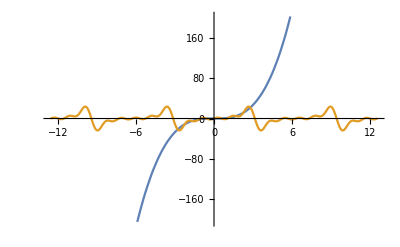

```mathematica
(*Problem 3*)
f3=x^3;
f3Fourier=FourierTrigSeries[f3,x,5]
Plot[{f3,f3Fourier},{x,-4π,4π}]
```

```mathematica
(*Problem 4*)
S4=({{0, a^2}, {b^2, 0}})
S999=MatrixPower[S,999]
Eigenvalues[S999]
Eigenvectors[S999]
```

{{0,a^2},{b^2,0}}

{{0,a^1000 b^998},{a^998 b^1000,0}}

{-a^999 b^999,a^999 b^999}

{{-a/b,1},{a/b,1}}

```mathematica
(*Problem 5*)
G5=GreenFunction[{y''[t]+y'[t]+4 π^2 y[t],y[0]==0,y'[0]==0},y[t],{t,0,∞},t5]//FullSimplify
G5Solution=Integrate[G5*(DiracDelta[t^2-3t+2]+DiracDelta[t/4-1]),{t5,0,t},Assumptions->t∈Reals]
```

(2 ⅇ^(1/2 (-t+t5)) HeavisideTheta[t-t5] Sin[1/2 √(-1+16 π^2) (t-t5)])/(√(-1+16 π^2))

1/π^2 DiracDelta[-4+t] HeavisideTheta[t] (1-ⅇ^(-t/2) Cos[1/2 √(-1+16 π^2) t]-(ⅇ^(-t/2) Sin[1/2 √(-1+16 π^2) t])/(√(-1+16 π^2)))+1/(4 π^2)DiracDelta[2-3 t+t^2] HeavisideTheta[t] (1+ⅇ^(-t/2) (-Cos[1/2 √(-1+16 π^2) t]-Sin[1/2 √(-1+16 π^2) t]/(√(-1+16 π^2))))

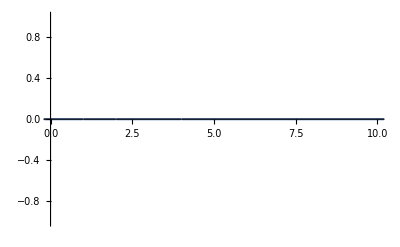

```mathematica
Plot[G5Solution,{t,-20,20},PlotRange->{{0,10},{-1,1}}]
```